```mathematica
Clear["Global`*"]
```

```mathematica
(*Built-in functions. *)

(*RowDelete takes a matrix and deletes the specified rows*)
RowDelete[x_,entries_]:=Module[{list},
list=Table[{entries[[i]]},{i,1,Length[entries]}];
Delete[x,list]
]

(*ColumnDelete takes a matrix and delete the specified columns*)
ColumnDelete[x_,entries_]:=Module[{},
Transpose[RowDelete[Transpose[x],entries]]
]

(*AddZeroToRow adds a zero to a row vector*)
AddZeroToRow[x_,j_]:=Module[{l},
l=Length[x];
Join[Take[x,j-1],{0},Take[x,-(l-j+1)]]
]

(*AddZerosToRow will add any number of zeros to a row vector*)
AddZerosToRow[x_,entries_]:=Module[{y,list},
y=x;
list=Sort[entries];
For[i=1,i≤Length[list],i++,
y=AddZeroToRow[y,list[[i]]]
];
y
]

(*Composite constrained and unconstrained estimates with covatiares. I.e., the most general case.*)

MAR[datasets_, cov_, constraints_]:=Module[{X,U,Y,Z,D,d0,p,x0,u0,y0,one,popdata,covdata,tanks,tankrow,index,tempdata,c},
p=Length[datasets[[1,1]]]-cov;

If[cov==0,
X={};Y={};
For[j=1,j≤Length[datasets],j++,
x0=Delete[datasets[[j]],Length[datasets[[j]]]];
y0=Delete[datasets[[j]],1];
X=Join[X,x0];
Y=Join[Y,y0]
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1].Inverse[Transpose[ColumnDelete[Z,c+1]].ColumnDelete[Z,c+1]]],c+1]};
D=Join[D,d0]
];
D,

X={};Y={};U={};
For[j=1,j≤Length[datasets],j++,
tempdata=datasets[[j]];
x0=tempdata[[All,cov+1;;cov+p]];
x0=Delete[x0,Length[x0]];
u0=tempdata[[All,1;;cov]];
u0=Delete[u0,Length[u0]];
y0=tempdata[[All,cov+1;;cov+p]];
y0=Delete[y0,1];

X=Join[X,x0];
U=Join[U,u0];
Y=Join[Y,y0];
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[U],Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1+cov].Inverse[Transpose[ColumnDelete[Z,c+1+cov]].ColumnDelete[Z,c+1+cov]]],c+1+cov]};
D=Join[D,d0]
];
D
]
]


(*Code to process raw data after it has been imported.*)
ProcessData[raw_,cov_]:=Module[{rawdata,p,tankrow,tanks,purepopdata,logpopdata,covdata,processeddata,index,compdataset},
rawdata=Delete[raw,1];
p=Length[rawdata[[1]]]-cov-1;

tankrow=Delete[raw[[All,1]],1];(*extracts the column of tank labels as a row vector.*)
tanks=DeleteDuplicates[tankrow];(*Just getting a list of tank labels*)

purepopdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤cov,i++,
purepopdata=ColumnDelete[purepopdata,{1}]
];
logpopdata=Log[purepopdata];

If[cov==0,covdata={},
covdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤p,i++,
covdata=ColumnDelete[covdata,{Length[covdata[[1]]]}]
]
];

processeddata=If[cov==0,Transpose[Join[{tankrow},Transpose[logpopdata]]],Transpose[Join[{tankrow},Transpose[covdata],Transpose[logpopdata]]]];(*Join log transformed values back up with tank labels*)

(*Below we extract tank specific processed data and label it by the tank label.*)
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
data[index]={};
For[i=1,i≤Length[processeddata],i++,
i0=If[processeddata[[i,1]]==index,{processeddata[[i]]},{}];
data[index]=Join[data[index],i0]
];
data[index]=ColumnDelete[data[index],{1}]
];

compdataset={};
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
compdataset=Join[compdataset,{data[index]}]
];
compdataset
]

(*Script to get sensitivity measures from the matrix output of MAR
and relative interaction strengths*)
B[D_]:=Module[{p,cov,B},(*extract B matrix*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]]
]

Sens[D_]:=Module[{p,cov,B,det,eig},
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
det=Det[B];
eig=Abs[Eigenvalues[B]][[1]];
{(det^2)^(1/p),eig,1/(1-eig^2)}
]

RIS[D_]:=Module[{p,cov,B,erow,e1,e2,e3,e4,rel}, (*row: top down control*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
erow=B[[-2]];(*Extract second to last row in B matrix*)
e1=Abs[Delete[erow,-2]];(*Delete second to last entry in erow (diagonal)*)
e2=Sort[e1];(*sorts small to large*)
e3=Delete[e2,-1];(*delete largest value*)
e4=Mean[e3];(*average of smaller values*)
rel=e4/Max[e1](*average/largest*)
]

RISd[D_]:=Module[{p,cov,B,erow,e2,e3,e4,rel}, (*row: top down control with diagonal entry*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
erow=B[[-2]];(*Extract second to last row in B matrix*)
e2=Abs[Sort[erow]];(*sorts small to large absolute value*)
e3=Delete[e2,-1];(*delete largest value*)
e4=Mean[e3];(*average of smaller values*)
rel=e4/Max[e2](*average/largest*)
]

bRIS[D_]:=Module[{p,cov,B,ecol,e1,e2,e3,e4,rel}, (*column: bottom up control*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
ecol=B[[All,-2]];(*Extract second to last column in B matrix*)
e1=Abs[Delete[ecol,-2]];(*Delete second to last entry in erow (diagonal)*)
e2=Sort[e1];(*sorts small to large*)
e3=Delete[e2,-1];(*delete largest value*)
e4=Mean[e3];(*average of smaller values*)
rel=e4/Max[e1](*average/largest*)
]

bRISd[D_]:=Module[{p,cov,B,ecol,e2,e3,e4,rel}, (*column: bottom up control with diagonal entry*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
ecol=B[[All,-2]];(*Extract second to last column in B matrix*)
e2=Abs[Sort[ecol]];(*sorts small to large*)
e3=Delete[e2,-1];(*delete largest value*)
e4=Mean[e3];(*average of smaller values*)
rel=e4/Max[e2](*average/largest*)
]
```

```mathematica
(*Here are some examples of using the code to import and process the data, compute estimates of the MAR process parameters, and compute sensitivities. The number of covariates must be specified. Note: zero covariates are possible (but this does NOT mean you can have covariates all of which a zero!).
Note, also, that this all works for any number of covariates as well as any number of raplicates (tanks), including only one tank. Check the data .csvs to see the exact format of the data*)

SetDirectory["/Users/JayneEllen/Dropbox/Weak interactions/tank data"];

(*Import various multi-tank data sets some with covariates, some without.*)
rawdata[1]=Import["CER.csv"];
rawdata[2]=Import["CER_DAP.csv"];
rawdata[3]=Import["CER_SCA.csv"];
rawdata[4]=Import["DAP.csv"];
rawdata[5]=Import["DAPSCA.csv"];
rawdata[6]=Import["SCA.csv"];
rawdata[7]=Import["N.csv"];
rawdata[8]=Import["N_CER.csv"];
rawdata[9]=Import["N_CER_DAP.csv"];
rawdata[10]=Import["N_CER_SCA.csv"];
rawdata[11]=Import["N_Dap.csv"];
rawdata[12]=Import["N_Sca.csv"];
rawdata[13]=Import["N_SCA_DAP.csv"];
rawdata[14]=Import["N_I_DAP.csv"];
(*1-14 have 1 cov*)
rawdata[15]=Import["N_I.csv"];
rawdata[16]=Import["N_I_cop.csv"];
(*15&16 have 2 covs*)
rawdata[17]=Import["CER0.csv"];
rawdata[18]=Import["CER_DAP0.csv"];
rawdata[19]=Import["CER_SCA0.csv"];
rawdata[20]=Import["DAP0.csv"];
rawdata[21]=Import["DAPSCA0.csv"];
rawdata[22]=Import["SCA0.csv"];
rawdata[23]=Import["N0.csv"];
rawdata[24]=Import["N_CER0.csv"];
rawdata[25]=Import["N_CER_DAP0.csv"];
rawdata[26]=Import["N_CER_SCA0.csv"];
rawdata[27]=Import["N_DAP0.csv"];
rawdata[28]=Import["N_SCA0.csv"];
rawdata[29]=Import["N_SCA_DAP0.csv"];
rawdata[30]=Import["N_I_DAP0.csv"];
rawdata[31]=Import["N_I0.csv"];
rawdata[32]=Import["N_I_COP0.csv"];
rawdata[33]=Import["CER_SCA_DAP0.csv"];
(*17-33 have no cov;
1-16 correspond to 17-32 respectively*)
```

```mathematica
For[h=1,h≤14,h++,
data[h]=ProcessData[rawdata[h],1];
m[h]=MAR[data[h],1,{}];
Print[h,MatrixForm[m[h]],Sens[m[h]]]
]
For[n=15,n≤16,n++,
data[n]=ProcessData[rawdata[n],2];
m[n]=MAR[data[n],2,{}];
Print[n,MatrixForm[m[n]],Sens[m[n]]]
]
For[o=17,o≤33,o++,
data[o]=ProcessData[rawdata[o],0];
m[o]=MAR[data[o],0,{}];
Print[o,MatrixForm[m[o]],Sens[m[o]]]
]
```

1(1.9975 | -0.0000805328 | 0.708019 | -0.407835 | 0.0861813
0.696552 | -0.00149718 | -0.0220461 | 0.812637 | -0.0626612
-0.943238 | 0.00091856 | -0.0615616 | 0.504379 | 0.0607315){0.150788,0.820758,3.06413}

2(2.65623 | -0.0092127 | 0.653258 | -0.203228 | -0.538855 | 0.0150064
3.19988 | 0.0046842 | -0.100671 | 0.464865 | -0.427035 | -0.0102269
1.30098 | -0.00110249 | -0.0156657 | -0.148924 | 0.586042 | -0.00910459
0.606979 | 0.00784031 | 0.0166469 | -0.138761 | 0.0182279 | 0.476508){0.22848,0.757578,2.347}

3(1.54934 | 0.00107001 | 0.763357 | 0.0281999 | -0.38131 | 0.114692
0.469094 | 0.00379858 | -0.0327169 | 0.832546 | 0.0253453 | -0.0182112
0.936064 | -0.00144269 | 0.0188309 | -0.107957 | 0.741617 | -0.0140196
-0.737737 | -0.00267826 | 0.0833472 | -0.167244 | 0.408306 | 0.145936){0.260601,0.825285,3.13573}

4(1.48799 | 0.00842099 | 0.694503 | 0.0643865 | -0.0390425
1.65364 | 0.000736089 | -0.216039 | 0.531799 | 0.0350598
0.423581 | -0.00015351 | -0.15048 | 0.0720728 | 0.469323){0.31317,0.627702,1.65019}

5(1.4191 | 0.00464424 | 0.766095 | -0.146635 | 0.187849 | -0.0420592
1.61903 | 0.0025446 | 0.137915 | 0.615732 | -0.00423738 | -0.0238562
2.09058 | -0.00131963 | -0.110815 | -0.184677 | 0.470612 | 0.056651
2.23422 | -0.0000193825 | -0.304766 | -0.288966 | 0.103176 | 0.511134){0.33539,0.761071,2.37659}

6(-0.263177 | 0.00247792 | 0.956029 | 0.133207 | -0.0577182
1.13106 | 0.000459637 | -0.0880767 | 0.77001 | -0.0212019
-0.259153 | -0.00393702 | -0.20041 | 0.463375 | 0.14534){0.232496,0.921152,6.60154}

7(0.50388 | 0.0147507 | 0.764972 | 0.143689 | -0.112012 | 0.169819 | -0.13057 | -0.0450889
1.11595 | -0.0206534 | 0.0296734 | 0.705844 | -0.238057 | -0.0937593 | 0.18902 | -0.119123
1.18343 | -0.00617705 | -0.0445223 | -0.0381735 | 0.65326 | -0.0909372 | 0.14572 | -0.0793196
0.560133 | 0.00360661 | 0.087021 | -0.00917747 | -0.105498 | 0.635721 | -0.0982118 | 0.0162848
0.995185 | -0.00365932 | 0.0225838 | 0.000675736 | -0.124985 | 0.00568141 | 0.559094 | -0.00780026
1.8578 | 0.000316469 | 0.135954 | 0.05692 | -0.414809 | 0.0693831 | -0.29071 | 0.504025){0.380784,0.889955,4.80817}

8(0.575223 | 0.000242853 | 0.865221 | -0.0738149 | 0.00191428 | 0.0830788 | 0.00428555
1.30521 | 0.00573995 | 0.0753252 | 0.713746 | -0.0188291 | -0.132686 | 0.0148278
0.46567 | 0.00337722 | 0.0597769 | -0.0830068 | 0.694512 | -0.167449 | 0.0498119
1.33486 | -0.0022681 | -0.0799712 | -0.126698 | 0.0376145 | 0.62878 | -0.0028047
1.39282 | -0.0117802 | -0.174497 | -0.179049 | 0.216746 | -0.149043 | 0.488269){0.438793,0.833306,3.27223}

9(2.77083 | 0.00587129 | 0.665639 | -0.0771092 | -0.335554 | 0.0845091
3.20636 | 0.0187722 | -0.276425 | 0.727909 | -0.372402 | 0.150861
0.833787 | -0.0017165 | -0.0639752 | 0.0952145 | 0.783098 | -0.0214015
-0.892985 | 0.00267492 | -0.141528 | 0.22266 | 0.430563 | 0.173818){0.245593,0.908567,5.73043}

10(2.70222 | -0.00242432 | 0.448082 | -0.236026 | -0.283745 | 0.269914
0.543538 | 0.0148901 | -0.081455 | 0.514519 | -0.214686 | 0.10347
1.64263 | 0.00394322 | -0.204113 | 0.04403 | 0.504742 | 0.058207
1.58302 | 0.0199188 | -0.331256 | 0.406965 | 0.263354 | 0.607252){0.211263,0.675425,1.83891}

11(2.81857 | -0.00640059 | 0.666437 | -0.15095 | 0.118321 | -0.387847 | -0.0488106
2.56275 | -0.00265923 | -0.132825 | 0.423208 | -0.028495 | 0.112579 | -0.10914
0.0154887 | -0.0114097 | 0.0511937 | -0.0800714 | 0.66027 | 0.0809096 | -0.0994937
0.846796 | -0.000937104 | 0.01907 | -0.128328 | -0.0332448 | 0.848403 | 0.0310534
0.739427 | -0.00705622 | 0.0310061 | -0.27328 | 0.131446 | 0.273537 | 0.473349){0.330821,0.849224,3.58655}

12(-0.769437 | -0.00512093 | 0.243673 | -0.166748 | -0.228116 | -0.594337 | -0.0275865
0.532973 | 0.000695038 | -0.226735 | 0.543917 | -0.31465 | -0.0875726 | -0.0339801
0.542994 | 0.00136057 | -0.314976 | -0.207129 | 0.771015 | -0.488445 | 0.0628495
1.3271 | 0.00581438 | 0.0426278 | -0.151315 | 0.0535802 | 0.555383 | 0.0199509
1.4919 | 0.0232288 | -0.397599 | -0.11549 | 0.939172 | -0.51115 | 0.402644){0.128051,0.995083,101.933}

13(2.16355 | -0.00186665 | 0.613874 | 0.281303 | -0.389806 | 0.23785
0.0988159 | 0.00753903 | 0.156486 | 0.626016 | -0.0206994 | -0.202846
1.27087 | 0.0110542 | -0.0846217 | 0.0936676 | 0.690763 | 0.00387858
-1.10446 | 0.00522028 | -0.0415164 | 0.0613434 | 0.530073 | -0.058413){0.1325,0.84939,3.59019}

14(1.72767 | 0.0108849 | 0.703269 | -0.0158518 | 0.156016 | -0.410694 | 0.0759976
0.394172 | -0.000844831 | 0.148688 | 0.673179 | -0.242003 | -0.232833 | 0.162897
0.871205 | 0.00631698 | 0.178223 | -0.135835 | 0.572527 | -0.108691 | 0.00534249
0.666423 | -0.00540132 | 0.0169618 | -0.0558995 | 0.0177304 | 0.75337 | 0.0498994
-0.400168 | 0.00115289 | 0.143713 | 0.0146604 | -0.150838 | 0.382805 | 0.465305){0.347054,0.820514,3.06038}

15(2.37392 | -0.00621005 | -0.164276 | 0.760017 | -0.0546533 | -0.123874 | -0.134511 | -0.282433 | -0.00867368
1.82704 | 0.00334969 | -1.37732 | -0.0141517 | 0.614759 | -0.0747268 | -0.125551 | 0.0805634 | -0.0684883
1.94452 | -0.00171922 | -0.465289 | -0.0628242 | 0.0168444 | 0.636739 | -0.0489335 | -0.190585 | 0.00957562
2.63912 | -0.00183962 | -0.343244 | -0.076985 | -0.0206306 | -0.160135 | 0.663277 | -0.269204 | 0.0178376
0.762205 | 0.00135747 | -0.0202464 | -0.00554581 | -0.0254312 | -0.0577617 | 0.00838359 | 0.609459 | 0.0173345
0.0247922 | -0.0029703 | -0.211944 | 0.0216656 | -0.1227 | -0.145789 | 0.123698 | 0.127256 | 0.561974){0.389067,0.814724,2.9742}

16(2.37217 | -0.00620997 | -0.160223 | 0.759366 | -0.0557457 | -0.122951 | -0.136144 | 0.00394695 | -0.281885 | -0.00896968
1.74584 | 0.00335366 | -1.18882 | -0.044426 | 0.563953 | -0.0318307 | -0.201533 | 0.183568 | 0.106072 | -0.0822552
1.93873 | -0.00171894 | -0.451854 | -0.0649819 | 0.0132235 | 0.639796 | -0.0543488 | 0.0130828 | -0.188767 | 0.00859445
2.61064 | -0.00183822 | -0.277117 | -0.0876052 | -0.0384533 | -0.145087 | 0.636623 | 0.0643951 | -0.260256 | 0.0130082
1.66929 | -0.00772544 | -0.560065 | -0.030996 | 0.0797401 | -0.162323 | -0.0049843 | 0.599731 | -0.16606 | 0.0170274
0.760315 | 0.00135756 | -0.0158595 | -0.00625036 | -0.0266136 | -0.0567634 | 0.00661531 | 0.004272 | 0.610052 | 0.0170141
0.0534028 | -0.0029717 | -0.278365 | 0.0323328 | -0.104798 | -0.160904 | 0.15047 | -0.0646808 | 0.118268 | 0.566824){0.366355,0.816501,3.00007}

17(1.99818 | 0.707983 | -0.407981 | 0.0861775
0.709162 | -0.0227186 | 0.80994 | -0.0627321
-0.950975 | -0.061149 | 0.506034 | 0.060775){0.150651,0.820138,3.05462}

18(2.68556 | 0.652889 | -0.199781 | -0.547799 | 0.0143667
3.18497 | -0.100484 | 0.463112 | -0.422487 | -0.00990171
1.30449 | -0.0157098 | -0.148511 | 0.584972 | -0.00918114
0.582014 | 0.0169602 | -0.141695 | 0.0258395 | 0.477052){0.228249,0.755993,2.33386}

19(1.53905 | 0.763174 | 0.0296916 | -0.381444 | 0.115476
0.43256 | -0.033368 | 0.837842 | 0.0248667 | -0.015428
0.949939 | 0.0190782 | -0.109968 | 0.741799 | -0.0150766
-0.711977 | 0.0838063 | -0.170977 | 0.408643 | 0.143974){0.260432,0.82696,3.16319}

20(1.42976 | 0.701802 | 0.0700136 | -0.0429422
1.64855 | -0.215401 | 0.53229 | 0.0347189
0.424643 | -0.150613 | 0.0719703 | 0.469394){0.315875,0.631465,1.6632}

21(1.4399 | 0.772746 | -0.157753 | 0.177625 | -0.0386822
1.63043 | 0.14156 | 0.609641 | -0.00983901 | -0.0220059
2.08467 | -0.112705 | -0.181518 | 0.473517 | 0.0556914
2.23413 | -0.304794 | -0.28892 | 0.103219 | 0.51112){0.336983,0.762569,2.38955}

22(-0.304315 | 0.960884 | 0.136546 | -0.0553679
1.12343 | -0.087176 | 0.77063 | -0.020766
-0.193791 | -0.208125 | 0.458071 | 0.141605){0.229025,0.924334,6.86785}

23(0.546754 | 0.759171 | 0.153041 | -0.122838 | 0.168116 | -0.134587 | -0.0430212
1.05592 | 0.0377953 | 0.69275 | -0.222899 | -0.0913744 | 0.194644 | -0.122018
1.16547 | -0.0420932 | -0.0420898 | 0.657793 | -0.0902239 | 0.147402 | -0.0801854
0.570616 | 0.0856027 | -0.00689089 | -0.108145 | 0.635304 | -0.0991939 | 0.0167904
0.984549 | 0.0240229 | -0.00164426 | -0.1223 | 0.00610397 | 0.560091 | -0.0083132
1.85872 | 0.135829 | 0.0571206 | -0.415042 | 0.0693465 | -0.290796 | 0.504069){0.377968,0.890679,4.83813}

24(0.574996 | 0.865286 | -0.0740824 | 0.00186644 | 0.0830856 | 0.00429898
1.29987 | 0.0768736 | 0.707424 | -0.0199597 | -0.132526 | 0.0151454
0.462525 | 0.060688 | -0.0867268 | 0.693847 | -0.167355 | 0.0499987
1.33697 | -0.0805831 | -0.124199 | 0.0380612 | 0.628717 | -0.00293017
1.40379 | -0.177675 | -0.166073 | 0.219066 | -0.149372 | 0.487617){0.436781,0.830539,3.22368}

25(2.82693 | 0.658413 | -0.0817397 | -0.336607 | 0.0809348
3.38575 | -0.299527 | 0.713104 | -0.375769 | 0.139433
0.817385 | -0.0618628 | 0.0965683 | 0.783406 | -0.0203566
-0.867424 | -0.14482 | 0.220551 | 0.430084 | 0.17219){0.241591,0.908998,5.75632}

26(2.75927 | 0.437817 | -0.233321 | -0.297483 | 0.27251
0.193145 | -0.0184104 | 0.497905 | -0.130306 | 0.087527
1.54984 | -0.187417 | 0.0396301 | 0.527087 | 0.053985
1.11429 | -0.24692 | 0.38474 | 0.376231 | 0.585925){0.212514,0.653698,1.74618}

27(2.86659 | 0.665715 | -0.153726 | 0.122151 | -0.394732 | -0.045472
2.5827 | -0.133125 | 0.422054 | -0.0269036 | 0.109719 | -0.107753
0.101088 | 0.0499067 | -0.0850189 | 0.667098 | 0.0686375 | -0.0935423
0.853826 | 0.0189643 | -0.128734 | -0.032684 | 0.847395 | 0.0315422
0.792365 | 0.0302102 | -0.276339 | 0.135668 | 0.265948 | 0.477029){0.331958,0.851116,3.62844}

28(-0.788013 | 0.216402 | -0.176229 | -0.24457 | -0.630029 | -0.0225107
0.535494 | -0.223034 | 0.545204 | -0.312417 | -0.0827282 | -0.034669
0.547929 | -0.30773 | -0.20461 | 0.775387 | -0.478962 | 0.0615009
1.34819 | 0.0735914 | -0.140549 | 0.072262 | 0.595909 | 0.0141877
1.57617 | -0.273898 | -0.0724805 | 1.01381 | -0.349245 | 0.379619){0.0938105,0.995368,108.195}

29(2.15844 | 0.613041 | 0.281667 | -0.389507 | 0.242239
0.119453 | 0.159847 | 0.624546 | -0.0219087 | -0.220574
1.30113 | -0.0796939 | 0.0915111 | 0.688989 | -0.0221153
-1.09017 | -0.0391893 | 0.060325 | 0.529235 | -0.0706884){0.125156,0.844345,3.48332}

30(1.60569 | 0.697882 | -0.00977014 | 0.168945 | -0.390628 | 0.070982
0.40364 | 0.149106 | 0.672707 | -0.243006 | -0.234391 | 0.163286
0.80041 | 0.175097 | -0.132306 | 0.580031 | -0.0970451 | 0.00243171
0.726956 | 0.0196345 | -0.0589173 | 0.0113149 | 0.743413 | 0.0523882
-0.413088 | 0.143142 | 0.0153046 | -0.149469 | 0.384931 | 0.464774){0.344105,0.819238,3.04091}

31(2.36347 | 0.756542 | -0.0415965 | -0.12627 | -0.139356 | -0.299924 | -0.00934921
1.47021 | -0.021253 | 0.729435 | -0.045208 | -0.185194 | 0.00537315 | -0.0550069
1.83782 | -0.0663569 | 0.0553167 | 0.644159 | -0.068104 | -0.219661 | 0.013145
2.56319 | -0.0798182 | 0.00769679 | -0.155173 | 0.649331 | -0.291391 | 0.0202734
0.750605 | -0.00512998 | -0.0236226 | -0.0561565 | 0.00705796 | 0.61004 | 0.0179846
-0.013185 | 0.0191867 | -0.105381 | -0.144368 | 0.115716 | 0.111191 | 0.562844){0.411363,0.816937,3.00649}

32(2.36125 | 0.754677 | -0.0458519 | -0.123756 | -0.143709 | 0.0117541 | -0.297593 | -0.0103386
1.4267 | -0.0578618 | 0.645882 | 0.00416358 | -0.270658 | 0.230787 | 0.0511309 | -0.074434
1.83185 | -0.0713819 | 0.0438479 | 0.650936 | -0.0798352 | 0.0316788 | -0.213381 | 0.0104784
2.54887 | -0.091869 | -0.0198069 | -0.138921 | 0.621198 | 0.0759696 | -0.276328 | 0.0138784
1.56376 | -0.0413458 | 0.116734 | -0.153265 | -0.0351033 | 0.623992 | -0.203542 | 0.0173275
0.749734 | -0.00586244 | -0.0252943 | -0.0551687 | 0.00534801 | 0.00461753 | 0.610956 | 0.0175959
-0.00322854 | 0.0275638 | -0.0862618 | -0.155665 | 0.135272 | -0.0528104 | 0.10072 | 0.567289){0.382188,0.816279,2.9968}

33(2.37103 | 0.627625 | 0.472445 | -0.463224 | -0.397761 | 0.229001
3.3731 | 0.460874 | -0.0370819 | -0.205036 | -0.57089 | 0.131739
1.26878 | 0.0224611 | 0.0493817 | 0.444969 | 0.3816 | -0.26667
0.626293 | 0.0904187 | -0.138616 | -0.0412865 | 0.684195 | 0.0590893
-2.58284 | 0.337446 | -0.533755 | 0.243174 | 0.766926 | -0.157582){0.166167,0.821852,3.0811}

```mathematica
(*Do covariates matter? subtract B matricies...*)
B[m[1]]-B[m[17]]
B[m[2]]-B[m[18]]
B[m[3]]-B[m[19]]
B[m[4]]-B[m[20]]
B[m[5]]-B[m[21]]
B[m[6]]-B[m[22]]
B[m[7]]-B[m[23]]
B[m[8]]-B[m[24]]
B[m[9]]-B[m[25]]
B[m[10]]-B[m[26]]
B[m[11]]-B[m[27]]
B[m[12]]-B[m[28]]
B[m[13]]-B[m[29]]
B[m[14]]-B[m[30]]
B[m[15]]-B[m[31]]
B[m[16]]-B[m[32]]
```

{{0.0000361738,0.00014508,3.8114×10^-6},{0.000672505,0.00269718,0.0000708575},{-0.000412599,-0.00165479,-0.0000434729}}

{{0.000368226,-0.00344784,0.0089439,0.000639653},{-0.000187224,0.00175305,-0.00454753,-0.000325231},{0.0000440656,-0.000412604,0.00107032,0.0000765474},{-0.000313372,0.00293423,-0.00761155,-0.000544366}}

{{0.000183416,-0.0014917,0.000134807,-0.000783985},{0.000651138,-0.0052956,0.000478574,-0.00278319},{-0.0002473,0.00201125,-0.000181761,0.00105705},{-0.000459098,0.00373377,-0.000337428,0.00196234}}

{{-0.00729889,-0.00562703,0.00389968},{-0.000638005,-0.000491866,0.000340876},{0.000133055,0.000102578,-0.0000710893}}

{{-0.00665134,0.0111176,0.0102237,-0.00337699},{-0.0036443,0.0060914,0.00560163,-0.00185027},{0.00188994,-0.00315901,-0.00290501,0.000959551},{0.000027759,-0.0000463988,-0.0000426682,0.0000140937}}

{{-0.00485528,-0.00333877,-0.00235035},{-0.00090062,-0.000619319,-0.000435975},{0.00771427,0.00530478,0.00373435}}

{{0.00580066,-0.00935185,0.0108259,0.00170335,0.00401679,-0.00206765},{-0.00812188,0.0130941,-0.0151581,-0.00238498,-0.00562417,0.00289506},{-0.00242911,0.00391622,-0.00453351,-0.000713303,-0.00168209,0.000865859},{0.00141829,-0.00228657,0.00264699,0.000416478,0.000982125,-0.000505551},{-0.00143902,0.00231999,-0.00268568,-0.000422565,-0.000996478,0.00051294},{0.000124451,-0.00020064,0.000232265,0.0000365447,0.0000861784,-0.0000443606}}

{{-0.0000655138,0.000267501,0.0000478365,-6.78079×10^-6,-0.0000134343},{-0.00154845,0.00632251,0.00113064,-0.000160267,-0.000317526},{-0.000911062,0.00371998,0.000665234,-0.0000942964,-0.000186823},{0.000611858,-0.00249829,-0.000446763,0.0000633283,0.000125468},{0.00317791,-0.0129758,-0.00232043,0.000328919,0.000651663}}

{{0.0072255,0.00463049,0.00105297,0.00357431},{0.023102,0.014805,0.00336663,0.0114281},{-0.0021124,-0.00135374,-0.000307839,-0.00104496},{0.00329188,0.00210962,0.000479723,0.00162843}}

{{0.0102646,-0.00270505,0.0137383,-0.00259575},{-0.0630446,0.0166143,-0.0843798,0.015943},{-0.0166956,0.00439983,-0.0223456,0.00422205},{-0.0843365,0.0222254,-0.112877,0.0213273}}

{{0.000721966,0.00277548,-0.00383036,0.00688439,-0.00333859},{0.000299953,0.00115312,-0.00159139,0.00286024,-0.00138707},{0.00128697,0.00494756,-0.00682797,0.0122721,-0.00595135},{0.000105702,0.000406356,-0.000560799,0.00100794,-0.0004888},{0.000795919,0.00305978,-0.00422271,0.00758958,-0.00368057}}

{{0.0272707,0.00948172,0.0164537,0.0356929,-0.00507584},{-0.00370132,-0.00128691,-0.00223318,-0.00484441,0.000688919},{-0.00724548,-0.00251917,-0.00437154,-0.00948314,0.00134859},{-0.0309636,-0.0107657,-0.0186818,-0.0405262,0.00576319},{-0.123701,-0.0430096,-0.0746348,-0.161905,0.0230243}}

{{0.000832114,-0.000364144,-0.000299428,-0.00438943},{-0.00336074,0.0014707,0.00120933,0.017728},{-0.00492772,0.00215643,0.00177319,0.0259939},{-0.00232709,0.00101837,0.000837382,0.0122755}}

{{0.00538607,-0.00608162,-0.0129288,-0.0200667,0.00501563},{-0.000418038,0.000472023,0.00100347,0.00155747,-0.000389287},{0.00312576,-0.00352942,-0.00750314,-0.0116455,0.00291078},{-0.00267267,0.00301782,0.00641554,0.00995746,-0.00248885},{0.000570474,-0.000644144,-0.00136938,-0.00212539,0.000531238}}

{{0.0034753,-0.0130568,0.00239669,0.00484578,0.0174907,0.000675534},{0.00710134,-0.114676,-0.0295189,0.0596428,0.0751903,-0.0134814},{0.00353262,-0.0384723,-0.0074198,0.0191704,0.0290768,-0.0035694},{0.00283321,-0.0283273,-0.00496207,0.013946,0.0221867,-0.00243576},{-0.000415832,-0.0018086,-0.00160516,0.00132563,-0.000581603,-0.000650144},{0.00247888,-0.0173191,-0.00142165,0.00798185,0.016065,-0.000870273}}

{{0.00468887,-0.0098938,0.000804493,0.00756482,-0.00780717,0.0157087,0.00136896},{0.0134357,-0.0819296,-0.0359943,0.0691247,-0.0472193,0.0549411,-0.00782125},{0.00640004,-0.0306244,-0.0111395,0.0254864,-0.018596,0.0246139,-0.00188392},{0.00426378,-0.0186464,-0.00616617,0.0154244,-0.0115745,0.0160727,-0.000870227},{0.0103498,-0.0369941,-0.00905756,0.030119,-0.0242614,0.0374824,-0.000300143},{-0.00038792,-0.00131926,-0.00159469,0.00126731,-0.000345533,-0.000903476,-0.000581836},{0.00476908,-0.0185365,-0.0052387,0.015198,-0.0118704,0.0175476,-0.000464891}}

```mathematica
(*" the relative difference due to presence of covariates which is a better indication of the effect of covariates on the B matrix estimates."*)
```

```mathematica
(B[m[1]]-B[m[17]])/B[m[1]]
(B[m[2]]-B[m[18]])/B[m[2]]
(B[m[3]]-B[m[19]])/B[m[3]]
(B[m[4]]-B[m[20]])/B[m[4]]
(B[m[5]]-B[m[21]])/B[m[5]]
(B[m[6]]-B[m[22]])/B[m[6]]
(B[m[7]]-B[m[23]])/B[m[7]]
(B[m[8]]-B[m[24]])/B[m[8]]
(B[m[9]]-B[m[25]])/B[m[9]]
(B[m[10]]-B[m[26]])/B[m[10]]
(B[m[11]]-B[m[27]])/B[m[11]]
(B[m[12]]-B[m[28]])/B[m[12]]
(B[m[13]]-B[m[29]])/B[m[13]]
(B[m[14]]-B[m[30]])/B[m[14]]
(B[m[15]]-B[m[31]])/B[m[15]]
(B[m[16]]-B[m[32]])/B[m[16]]
```

{{0.0000510916,-0.000355733,0.0000442254},{-0.0305045,0.00331905,-0.0011308},{0.00670222,-0.00328085,-0.000715822}}

{{0.000563676,0.0169653,-0.016598,0.0426254},{0.00185976,0.0037711,0.0106491,0.0318014},{-0.00281286,0.00277056,0.00182635,-0.00840756},{-0.0188247,-0.021146,-0.417577,-0.00114241}}

{{0.000240276,-0.0528972,-0.000353538,-0.00683554},{-0.0199022,-0.00636073,0.0188822,0.152828},{-0.0131326,-0.0186301,-0.000245087,-0.075398},{-0.00550826,-0.0223253,-0.00082641,0.0134466}}

{{-0.0105095,-0.0873945,-0.099883},{0.0029532,-0.00092491,0.00972272},{-0.000884203,0.00142325,-0.000151472}}

{{-0.00868214,-0.0758181,0.0544253,0.0802913},{-0.0264242,0.00989295,-1.32196,0.0775594},{-0.0170549,0.0171056,-0.00617283,0.0169379},{-0.0000910832,0.000160568,-0.000413548,0.0000275734}}

{{-0.00507859,-0.0250645,0.0407212},{0.0102254,-0.000804299,0.020563},{-0.0384924,0.0114481,0.0256939}}

{{0.00758284,-0.065084,-0.0966494,0.0100304,-0.0307635,0.0458573},{-0.273709,0.018551,0.0636742,0.0254372,-0.0297544,-0.0243032},{0.0545593,-0.10259,-0.00693983,0.00784391,-0.0115433,-0.0109161},{0.0162982,0.249151,-0.0250904,0.000655128,-0.0100001,-0.0310444},{-0.0637189,3.43328,0.0214879,-0.0743768,-0.00178231,-0.0657594},{0.000915387,-0.00352494,-0.000559933,0.000526709,-0.000296441,-0.0000880126}}

{{-0.0000757192,-0.00362394,0.0249893,-0.0000816188,-0.00313479},{-0.0205569,0.0088582,-0.0600475,0.00120787,-0.0214142},{-0.015241,-0.0448153,0.000957844,0.000563135,-0.00375057},{-0.00765097,0.0197185,-0.0118774,0.000100716,-0.0447348},{-0.0182118,0.0724708,-0.0107058,-0.00220688,0.00133464}}

{{0.010855,-0.0600511,-0.00313799,0.0422949},{-0.0835741,0.0203391,-0.00904031,0.0757525},{0.0330191,-0.0142178,-0.000393104,0.0488266},{-0.0232596,0.0094746,0.00111417,0.00936857}}

{{0.0229079,0.0114608,-0.0484177,-0.00961696},{0.773981,0.0322909,0.393038,0.154083},{0.0817961,0.0999281,-0.0442714,0.0725351},{0.254596,0.0546124,-0.428614,0.0351211}}

{{0.00108332,-0.0183867,-0.0323726,-0.0177503,0.0683989},{-0.00225826,0.00272472,0.055848,0.0254064,0.0127091},{0.0251393,-0.0617894,-0.0103412,0.151676,0.0598164},{0.00554286,-0.00316655,0.0168688,0.00118804,-0.0157406},{0.0256697,-0.0111965,-0.0321251,0.0277461,-0.00777561}}

{{0.111915,-0.0568627,-0.0721285,-0.060055,0.183997},{0.0163244,-0.002366,0.00709734,0.0553188,-0.0202742},{0.0230033,0.0121624,-0.00566984,0.019415,0.0214574},{-0.726371,0.0711475,-0.348669,-0.0729698,0.288869},{0.311121,0.372409,-0.0794688,0.316746,0.0571828}}

{{0.00135551,-0.00129449,0.000768147,-0.0184546},{-0.0214763,0.0023493,-0.0584234,-0.0873963},{0.0582324,0.0230222,0.00256701,6.70191},{0.0560524,0.0166011,0.00157975,-0.21015}}

{{0.00765863,0.383656,-0.0828684,0.0488603,0.0659972},{-0.00281151,0.000701185,-0.00414652,-0.0066892,-0.00238977},{0.0175385,0.0259831,-0.0131053,0.107144,0.544836},{-0.15757,-0.0539866,0.361837,0.0132172,-0.0498775},{0.00396954,-0.0439376,0.00907843,-0.00555213,0.0011417}}

{{0.00457266,0.238902,-0.0193479,-0.0360253,-0.0619288,-0.0778833},{-0.501801,-0.186538,0.395023,-0.475049,0.933305,0.196843},{-0.0562302,-2.28398,-0.0116528,-0.391764,-0.152567,-0.37276},{-0.0368021,1.37308,0.0309868,0.0210259,-0.082416,-0.136552},{0.0749813,0.0711173,0.0277894,0.158122,-0.000954295,-0.0375058},{0.114416,0.14115,0.00975141,0.0645271,0.126242,-0.0015486}}

{{0.00617471,0.177481,-0.00654318,-0.0555647,-1.97802,-0.0557276,-0.152621},{-0.302429,-0.145277,1.1308,-0.342994,-0.257231,0.517961,0.0950851},{-0.0984896,-2.31591,-0.0174111,-0.468941,-1.4214,-0.130393,-0.219202},{-0.0486704,0.484911,0.0424997,0.0242284,-0.179742,-0.0617574,-0.0668984},{-0.333907,-0.463933,0.0557996,-6.04278,-0.0404538,-0.225716,-0.017627},{0.0620636,0.0495709,0.0280937,0.191572,-0.0808831,-0.00148098,-0.0341973},{0.147499,0.176878,0.032558,0.101003,0.183523,0.148372,-0.000820168}}

```mathematica
(*Top down relative interaction strength*)
For[r=1,r≤33,r++,
RIS[m[r]];
RISd[m[r]];
bRIS[m[r]];
bRISd[m[r]];
Print[r"top↓ = ",RIS[m[r]]]
Print[r"top↓ with diagonal= ",RISd[m[r]]]
Print[r"bottom↑ = ",bRIS[m[r]]]
Print[r"bottom↑ with diagonal= ",bRISd[m[r]]]
]
```

top↓ = 0.35183

top↓ with diagonal= 0.0521188

bottom↑ = 0.808589

bottom↑ with diagonal= 0.561268

2 top↓ = 0.0831643

2 top↓ with diagonal= 0.0987952

2 bottom↑ = 0.413156

2 bottom↑ with diagonal= 0.559754

3 top↓ = 0.152146

3 top↓ with diagonal= 0.0632885

3 bottom↑ = 0.497979

3 bottom↑ with diagonal= 0.366299

4 top↓ = 0.162285

4 top↓ with diagonal= 0.236084

4 bottom↑ = 0.893354

4 bottom↑ with diagonal= 0.1283

5 top↓ = 0.453401

5 top↓ with diagonal= 0.249422

5 bottom↑ = 0.285904

5 bottom↑ with diagonal= 0.209133

6 top↓ = 0.240721

6 top↓ with diagonal= 0.0709592

6 bottom↑ = 0.287471

6 bottom↑ with diagonal= 0.387386

7 top↓ = 0.0734911

7 top↓ with diagonal= 0.0578531

7 bottom↑ = 0.484608

7 bottom↑ with diagonal= 0.305577

8 top↓ = 0.316739

8 top↓ with diagonal= 0.098241

8 bottom↑ = 0.726207

8 bottom↑ with diagonal= 0.211623

9 top↓ = 0.448339

9 top↓ with diagonal= 0.0768705

9 bottom↑ = 0.822127

9 bottom↑ with diagonal= 0.484622

10 top↓ = 0.250443

10 top↓ with diagonal= 0.202314

10 bottom↑ = 0.842375

10 bottom↑ with diagonal= 0.503085

11 top↓ = 0.21655

11 top↓ with diagonal= 0.0623806

11 bottom↑ = 0.401383

11 bottom↑ with diagonal= 0.251907

12 top↓ = 0.255887

12 top↓ with diagonal= 0.120401

12 bottom↑ = 0.609737

12 bottom↑ with diagonal= 0.707303

13 top↓ = 0.472417

13 top↓ with diagonal= 0.0879066

13 bottom↑ = 0.387216

13 bottom↑ with diagonal= 0.453884

14 top↓ = 0.504427

14 top↓ with diagonal= 0.0466209

14 bottom↑ = 0.58789

14 bottom↑ with diagonal= 0.376649

15 top↓ = 0.245384

15 top↓ with diagonal= 0.0375601

15 bottom↑ = 0.590943

15 bottom↑ with diagonal= 0.311766

16 top↓ = 0.214101

16 top↓ with diagonal= 0.0321089

16 bottom↑ = 0.595578

16 bottom↑ with diagonal= 0.306342

17 top↓ = 0.362153

17 top↓ with diagonal= 0.0527512

17 bottom↑ = 0.806232

17 bottom↑ with diagonal= 0.564248

18 top↓ = 0.0838014

18 top↓ with diagonal= 0.0988096

18 bottom↑ = 0.409207

18 bottom↑ with diagonal= 0.56762

19 top↓ = 0.155294

19 top↓ with diagonal= 0.0647629

19 bottom↑ = 0.497147

19 bottom↑ with diagonal= 0.366206

20 top↓ = 0.161183

20 top↓ with diagonal= 0.234946

20 bottom↑ = 0.972812

20 bottom↑ with diagonal= 0.133371

21 top↓ = 0.463855

21 top↓ with diagonal= 0.246323

21 bottom↑ = 0.318248

21 bottom↑ with diagonal= 0.204627

22 top↓ = 0.238207

22 top↓ with diagonal= 0.0700349

22 bottom↑ = 0.298089

22 bottom↑ with diagonal= 0.385799

23 top↓ = 0.0819386

23 top↓ with diagonal= 0.0579849

23 bottom↑ = 0.495043

23 bottom↑ with diagonal= 0.309458

24 top↓ = 0.326288

24 top↓ with diagonal= 0.0977284

24 bottom↑ = 0.726965

24 bottom↑ with diagonal= 0.211676

25 top↓ = 0.425706

25 top↓ with diagonal= 0.0760728

25 bottom↑ = 0.828182

25 bottom↑ with diagonal= 0.486108

26 top↓ = 0.249751

26 top↓ with diagonal= 0.177726

26 bottom↑ = 0.568521

26 bottom↑ with diagonal= 0.508467

27 top↓ = 0.215407

27 top↓ with diagonal= 0.0625223

27 bottom↑ = 0.375195

27 bottom↑ with diagonal= 0.247534

28 top↓ = 0.37956

28 top↓ with diagonal= 0.126106

28 bottom↑ = 0.481954

28 bottom↑ with diagonal= 0.611465

29 top↓ = 0.556267

29 top↓ with diagonal= 0.0935285

29 bottom↑ = 0.388689

29 bottom↑ with diagonal= 0.455087

30 top↓ = 0.471495

30 top↓ with diagonal= 0.0478385

30 bottom↑ = 0.611295

30 bottom↑ with diagonal= 0.372268

31 top↓ = 0.239488

31 top↓ with diagonal= 0.0360474

31 bottom↑ = 0.523146

31 bottom↑ with diagonal= 0.304091

32 top↓ = 0.212868

32 top↓ with diagonal= 0.031068

32 bottom↑ = 0.567957

32 bottom↑ with diagonal= 0.311724

33 top↓ = 0.458808

33 top↓ with diagonal= 0.120364

33 bottom↑ = 0.586867

33 bottom↑ with diagonal= 0.663182

Species count, λ

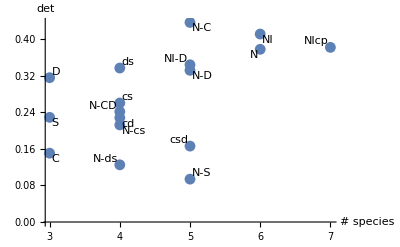

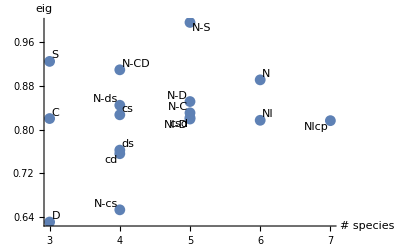

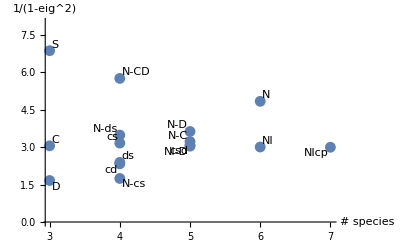

Excluded from plot: N-S =

{5,101.933}

Species count, top↓ relative interaction strength

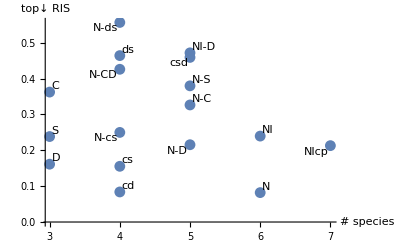

Species count, top↓ with diagonal relative interaction strength

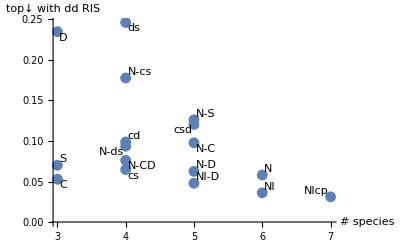

Species count, bottom↑ relative interaction strength

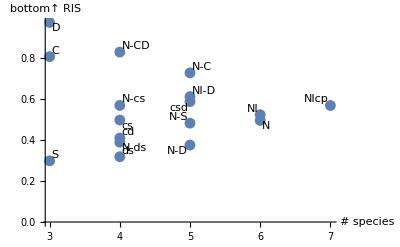

Species count, bottom↑ relative interaction strength

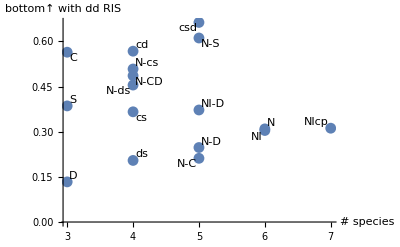

top↓ relative interaction strength , λ

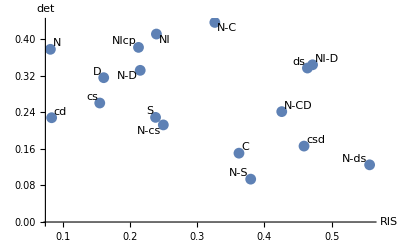

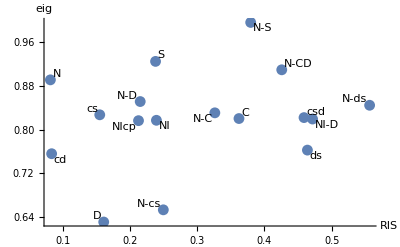

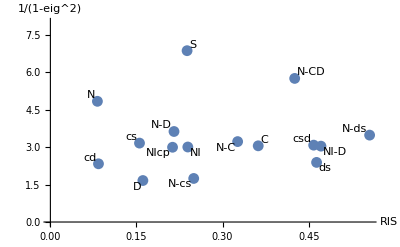

Excluded from plot: N-S =

{0.255887,101.933}

top↓ with dd relative interaction strength , λ

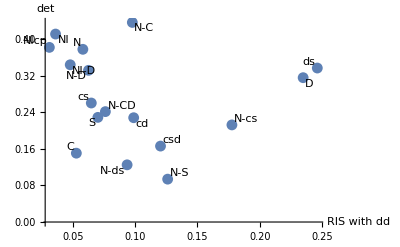

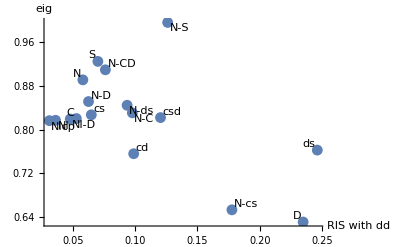

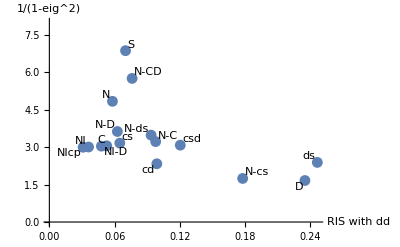

Excluded from plot: N-S =

{0.120401,101.933}

bottom↑ relative interaction strength , λ

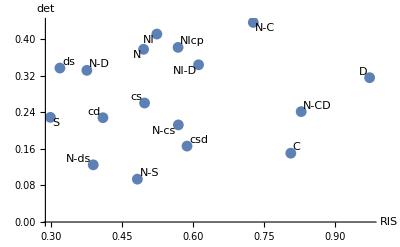

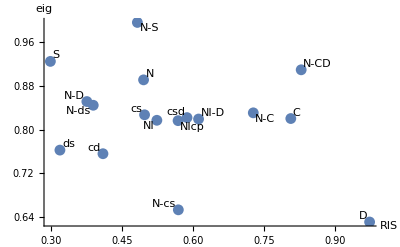

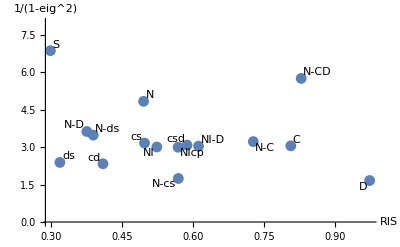

Excluded from plot: N-S =

{0.609737,101.933}

bottom↑ with dd relative interaction strength , λ

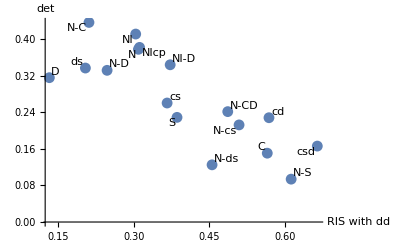

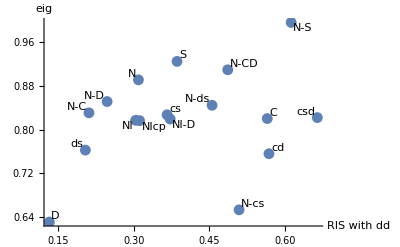

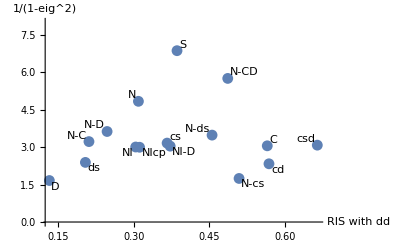

Excluded from plot: N-S =

{0.707303,101.933}

```mathematica
(*Plot Sens measures against species count*)
pdet={};
peig={};
psens3={};
pRIS={};
pRISd={};
pbRIS={};
pbRISd={};
RISdet={};
RISeig={};
RISsens3={};
RISddet={};
RISdeig={};
RISdsens3={};
bRISdet={};
bRISeig={};
bRISsens3={};
bRISddet={};
bRISdeig={};
bRISdsens3={};
comm={"C","cd","cs","D","ds","S","N","N-C","N-CD","N-cs","N-D","N-S","N-ds","NI-D","NI","NIcp","csd"};

For [z=17,z≤33,z++,
p=Length[m[z]];
rel=RIS[m[z]];
reld=RISd[m[z]];
brel=bRIS[m[z]];
breld=bRISd[m[z]];
det=Sens[m[z]][[1]];
eig=Sens[m[z]][[2]]; 
sens3=Sens[m[z]][[3]];

pdet=Join[pdet,{{p,det}}];
peig=Join[peig,{{p,eig}}];
psens3=Join[psens3,{{p,sens3}}];
pRIS=Join[pRIS,{{p,rel}}];
pRISd=Join[pRISd,{{p,reld}}];
pbRIS=Join[pbRIS,{{p,brel}}];
pbRISd=Join[pbRISd,{{p,breld}}];
RISdet=Join[RISdet,{{rel,det}}];
RISeig=Join[RISeig,{{rel,eig}}];
RISsens3=Join[RISsens3,{{rel,sens3}}];
RISddet=Join[RISddet,{{reld,det}}];
RISdeig=Join[RISdeig,{{reld,eig}}];
RISdsens3=Join[RISdsens3,{{reld,sens3}}];
bRISdet=Join[bRISdet,{{brel,det}}];
bRISeig=Join[bRISeig,{{brel,eig}}];
bRISsens3=Join[bRISsens3,{{brel,sens3}}];
bRISddet=Join[bRISddet,{{breld,det}}];
bRISdeig=Join[bRISdeig,{{breld,eig}}];
bRISdsens3=Join[bRISdsens3,{{breld,sens3}}];
]

Style["
Species count, λ",FontSize->20]
ListPlot[MapThread[Labeled,{pdet,comm}],AxesLabel->{"# species","det"},PlotRange->All]
ListPlot[MapThread[Labeled,{peig,comm}],AxesLabel->{"# species","eig"},PlotRange->All]
ListPlot[MapThread[Labeled,{psens3,comm}],AxesLabel->{"# species","1/(1-eig^2)"},PlotRange->{0,8}]
Print["Excluded from plot: N-S ="] 
Print[{Length[m[12]],Sens[m[12]][[3]]}]

Style["
Species count, top↓ relative interaction strength",FontSize->20]
ListPlot[MapThread[Labeled,{pRIS,comm}],AxesLabel->{"# species","top↓ RIS"},PlotRange->All]

Style["
Species count, top↓ with diagonal relative interaction strength",FontSize->20]
ListPlot[MapThread[Labeled,{pRISd,comm}],AxesLabel->{"# species","top↓ with dd RIS"},PlotRange->All]

Style["
Species count, bottom↑ relative interaction strength",FontSize->20]
ListPlot[MapThread[Labeled,{pbRIS,comm}],AxesLabel->{"# species","bottom↑ RIS"},PlotRange->All]

Style["
Species count, bottom↑ relative interaction strength",FontSize->20]
ListPlot[MapThread[Labeled,{pbRISd,comm}],AxesLabel->{"# species","bottom↑ with dd RIS"},PlotRange->All]


Style["
top↓ relative interaction strength , λ",FontSize->20]
ListPlot[MapThread[Labeled,{RISdet,comm}],AxesLabel->{"RIS","det"},PlotRange->All]
ListPlot[MapThread[Labeled,{RISeig,comm}],AxesLabel->{"RIS","eig"},PlotRange->All]
ListPlot[MapThread[Labeled,{RISsens3,comm}],AxesLabel->{"RIS","1/(1-eig^2)"},PlotRange->{0,8}]
Print["Excluded from plot: N-S ="] 
Print[{RIS[m[12]],Sens[m[12]][[3]]}]

Style["
top↓ with dd relative interaction strength , λ",FontSize->20]
ListPlot[MapThread[Labeled,{RISddet,comm}],AxesLabel->{"RIS with dd","det"},PlotRange->All]
ListPlot[MapThread[Labeled,{RISdeig,comm}],AxesLabel->{"RIS with dd","eig"},PlotRange->All]
ListPlot[MapThread[Labeled,{RISdsens3,comm}],AxesLabel->{"RIS with dd","1/(1-eig^2)"},PlotRange->{0,8}]
Print["Excluded from plot: N-S ="] 
Print[{RISd[m[12]],Sens[m[12]][[3]]}]


Style["
bottom↑ relative interaction strength , λ",FontSize->20]
ListPlot[MapThread[Labeled,{bRISdet,comm}],AxesLabel->{"RIS","det"},PlotRange->All]
ListPlot[MapThread[Labeled,{bRISeig,comm}],AxesLabel->{"RIS","eig"},PlotRange->All]
ListPlot[MapThread[Labeled,{bRISsens3,comm}],AxesLabel->{"RIS","1/(1-eig^2)"},PlotRange->{0,8}]
Print["Excluded from plot: N-S ="]
Print[{bRIS[m[12]],Sens[m[12]][[3]]}]

Style["
bottom↑ with dd relative interaction strength , λ",FontSize->20]
ListPlot[MapThread[Labeled,{bRISddet,comm}],AxesLabel->{"RIS with dd","det"},PlotRange->All]
ListPlot[MapThread[Labeled,{bRISdeig,comm}],AxesLabel->{"RIS with dd","eig"},PlotRange->All]
ListPlot[MapThread[Labeled,{bRISdsens3,comm}],AxesLabel->{"RIS with dd","1/(1-eig^2)"},PlotRange->{0,8}]
Print["Excluded from plot: N-S ="]
Print[{bRISd[m[12]],Sens[m[12]][[3]]}]
```

### Coefficient of variation for herbivore community built-in function

```mathematica
CV[Q_]:=Module[{c1,Hs,meanHs,totalHs,wHs,popCV,wCVpop,wAvg,comm,commCV},
c1=Delete[rawdata[Q],1];
Hs=c1[[All,2;;-3]];(*This will only work for 0 cov treatments, it extracts the herbivore columns*)
meanHs=Total[Hs]/Length[Hs];(*total of each herbivore species down column / # of rows*)
totalHs=Total[meanHs];
(*Adds the mean of each herbivore species together*)
wHs=meanHs/totalHs;
(*This gives the weight of each species*)
popCV=StandardDeviation[Hs]/Mean[Hs];
wCVpop=popCV*wHs;(*weighted population CV*)
wAvg=Total[wCVpop];(*weighted average*)

comm=Total[Hs,{2}];(*totals hs by row = total herbivore*)
commCV=StandardDeviation[comm]/Mean[comm];
{wAvg,commCV}
]
```

```mathematica
For[c=17,c≤33,c++,
Print[c"CV pop,comm = ",CV[c]]
]
```

17 CV pop,comm = {1.64441,1.01145}

18 CV pop,comm = {2.0259,1.87502}

19 CV pop,comm = {1.50713,0.990979}

20 CV pop,comm = {2.32617,1.62016}

21 CV pop,comm = {1.29929,1.2375}

22 CV pop,comm = {1.26459,0.823483}

23 CV pop,comm = {1.51047,1.46753}

24 CV pop,comm = {1.74714,0.940844}

25 CV pop,comm = {1.46971,0.954023}

26 CV pop,comm = {1.53618,0.973854}

27 CV pop,comm = {1.42433,1.20637}

28 CV pop,comm = {2.14325,1.377}

29 CV pop,comm = {1.84892,1.68448}

30 CV pop,comm = {3.01858,2.79321}

31 CV pop,comm = {2.48685,1.78469}

32 CV pop,comm = {1.77317,1.07088}

33 CV pop,comm = {1.8595,1.04082}

Community CV, λ

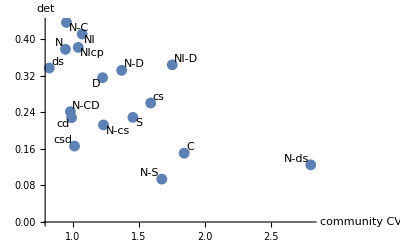

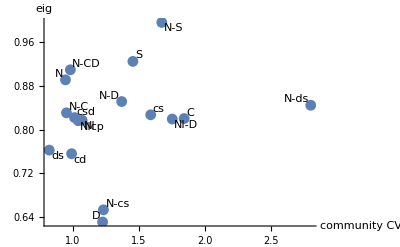

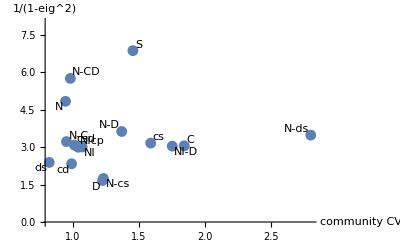

Excluded from plot: N-S

{1.68448,101.933}

Weighted Average, λ

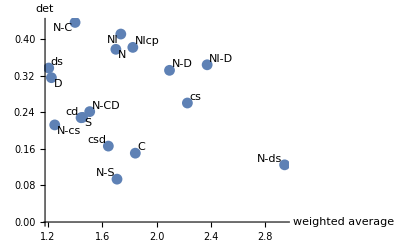

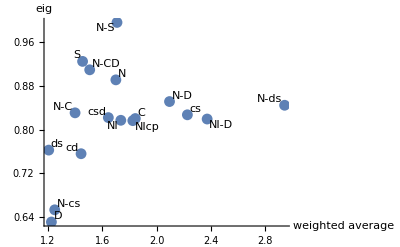

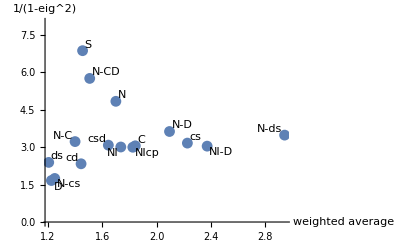

Excluded from plot: N-S

{1.84892,101.933}

Community CV, top↓ RIS

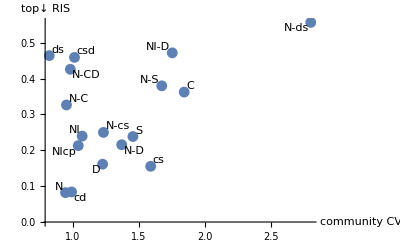

Community CV, top↓ with dd RIS

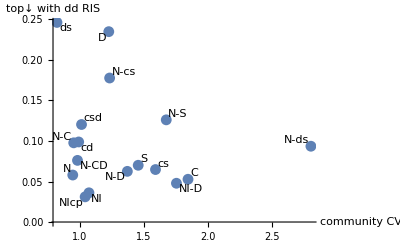

Community CV, bottom↑ RIS

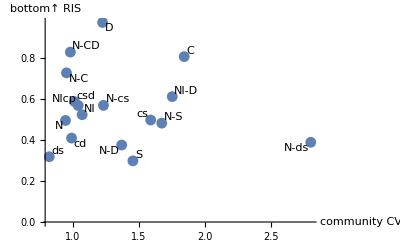

Community CV, bottom↑ with dd RIS

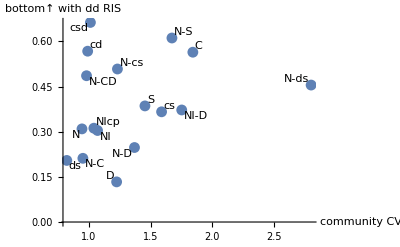

Weighted Average, top↓ RIS

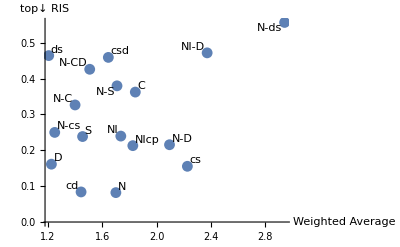

Weighted Average, top↓ with dd RIS

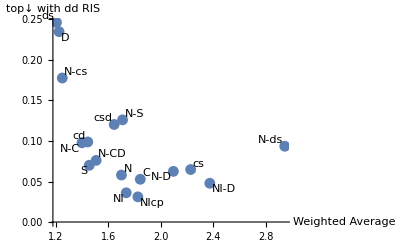

Weighted Average, bottom↑ RIS

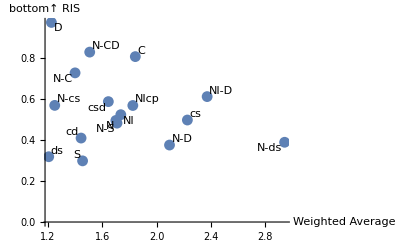

Weighted Average, bottom↑ with dd RIS

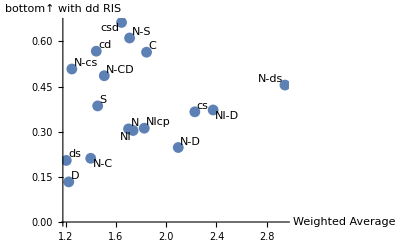

```mathematica
commCVdet={};
commCVeig={};
commCVsens3={};
popCVdet={};
popCVeig={};
popCVsens3={};
commCVRIS={};
commCVRISd={};
commCVbRIS={};
commCVbRISd={};
popCVRIS={};
popCVRISd={};
popCVbRIS={};
popCVbRISd={};
(*comm label list already defined - overlap badly so need to rethink point labels*)

For [v=17,v≤33,v++,
commCV=CV[v][[2]];
popCV=CV[v][[1]];
rel=RIS[m[v]];
reld=RISd[m[v]];
brel=bRIS[m[v]];
breld=bRISd[m[v]];
det=Sens[m[v]][[1]];
eig=Sens[m[v]][[2]]; 
sens3=Sens[m[v]][[3]];

commCVdet=Join[commCVdet,{{commCV,det}}];
commCVeig=Join[commCVeig,{{commCV,eig}}];
commCVsens3=Join[commCVsens3,{{commCV,sens3}}];
popCVdet=Join[popCVdet,{{popCV,det}}];
popCVeig=Join[popCVeig,{{popCV,eig}}];
popCVsens3=Join[popCVsens3,{{popCV,sens3}}];
commCVRIS=Join[commCVRIS,{{commCV,rel}}];
commCVRISd=Join[commCVRISd,{{commCV,reld}}];
commCVbRIS=Join[commCVbRIS,{{commCV,brel}}];
commCVbRISd=Join[commCVbRISd,{{commCV,breld}}];
popCVRIS=Join[popCVRIS,{{popCV,rel}}];
popCVRISd=Join[popCVRISd,{{popCV,reld}}];
popCVbRIS=Join[popCVbRIS,{{popCV,brel}}];
popCVbRISd=Join[popCVbRISd,{{popCV,breld}}];
]

Style["
Community CV, λ",FontSize->20]
ListPlot[MapThread[Labeled,{commCVdet,comm}],AxesLabel->{"community CV","det"}]
ListPlot[MapThread[Labeled,{commCVeig,comm}],AxesLabel->{"community CV","eig"}]
ListPlot[MapThread[Labeled,{commCVsens3,comm}],AxesLabel->{"community CV","1/(1-eig^2)"},PlotRange->{0,8}]
Print["Excluded from plot: N-S"] 
Print[{CV[12][[2]],Sens[m[12]][[3]]}]

Style["
Weighted Average, λ",FontSize->20]
ListPlot[MapThread[Labeled,{popCVdet,comm}],AxesLabel->{"weighted average","det"}]
ListPlot[MapThread[Labeled,{popCVeig,comm}],AxesLabel->{"weighted average","eig"}]
ListPlot[MapThread[Labeled,{popCVsens3,comm}],AxesLabel->{"weighted average","1/(1-eig^2)"},PlotRange->{0,8}]
Print["Excluded from plot: N-S"]
Print[{CV[12][[1]],Sens[m[12]][[3]]}] 

Style["
Community CV, top↓ RIS",FontSize->20]
ListPlot[MapThread[Labeled,{commCVRIS,comm}],AxesLabel->{"community CV","top↓ RIS"}]
Style["
Community CV, top↓ with dd RIS",FontSize->20]
ListPlot[MapThread[Labeled,{commCVRISd,comm}],AxesLabel->{"community CV","top↓ with dd RIS"}]
Style["
Community CV, bottom↑ RIS",FontSize->20]
ListPlot[MapThread[Labeled,{commCVbRIS,comm}],AxesLabel->{"community CV","bottom↑ RIS"}]
Style["
Community CV, bottom↑ with dd RIS",FontSize->20]
ListPlot[MapThread[Labeled,{commCVbRISd,comm}],AxesLabel->{"community CV","bottom↑ with dd RIS"}]

Style["
Weighted Average, top↓ RIS",FontSize->20]
ListPlot[MapThread[Labeled,{popCVRIS,comm}],AxesLabel->{"Weighted Average","top↓ RIS"}]
Style["
Weighted Average, top↓ with dd RIS",FontSize->20]
ListPlot[MapThread[Labeled,{popCVRISd,comm}],AxesLabel->{"Weighted Average","top↓ with dd RIS"}]
Style["
Weighted Average, bottom↑ RIS",FontSize->20]
ListPlot[MapThread[Labeled,{popCVbRIS,comm}],AxesLabel->{"Weighted Average","bottom↑ RIS"}]
Style["
Weighted Average, bottom↑ with dd RIS",FontSize->20]
ListPlot[MapThread[Labeled,{popCVbRISd,comm}],AxesLabel->{"Weighted Average","bottom↑ with dd RIS"}]
```